```mathematica
Compute2DShape[order_,eltype_]:=Block[{zeta1,zeta2,zeta3,a,b,xi,eta,psis,dpsis},
If[eltype==1,
If[order==1,
psis={
1/4(1-xi)(1-eta),
1/4(1+xi)(1-eta),
1/4 (1+xi)(1+eta),
1/4(1-xi)(1+eta)
};
,
psis={
xi eta(xi-1)(eta-1)/4,xi eta(xi+1)(eta-1)/4,xi eta(xi+1)(eta+1)/4,xi eta(xi-1)(eta+1)/4,-eta(xi+1)(xi-1)(eta-1)/2,-xi(xi+1)(eta+1)(eta-1)/2,-eta(xi+1)(xi-1)(eta+1)/2,-xi(xi-1)(eta+1)(eta-1)/2,(xi+1)(xi-1)(eta+1)(eta-1)
};
];
,
zeta1=1-xi-eta;
zeta2=xi;
zeta3=eta;
If[order==1,
psis={zeta1,zeta2,zeta3};
,
psis={
2*zeta1*(zeta1-1/2),2*zeta2*(zeta2-1/2),2*zeta3*(zeta3-1/2),4*zeta1*zeta2,4*zeta2*zeta3,4*zeta3*zeta1
};
];
];
dpsis=Transpose[Table[{D[psis[[i]],xi],D[psis[[i]],eta]},{i,1,Length[psis]}]];
{psis,dpsis}
];
```

```mathematica
<<NumericalDifferentialEquationAnalysis`
IntegrationRule[porder_,eltype_]:=Block[{pts,w,npts,matpsts},
If[eltype==1,
{pts,w}=Transpose[GaussianQuadratureWeights[porder+1,-1,1]];
npts=Length[pts];
matpsts=Flatten[Table[{pts[[j]],pts[[i]],w[[j]]w[[i]]},{i,npts,1,-1},{j,1,npts}],1];
,
If[porder==1,
matpsts={{1/3,1/3,1/2}};
];
If[porder==2,matpsts={{1/6,1/6,1/2 1/3},{2/3,1/6,1/2 1/3},{1/6,2/3,1/2 1/3}};
];
];
N[matpsts]
];
```

```mathematica
Contribute[data_]:=Block[{psis,GradPsi,Jac,x,y,nnodes,GradPhi,DetJ,InvJac,B,C,ek,ef,elcoords,weight},{psis,GradPsi,elcoords,weight}=data;
{x,y}=psis.elcoords;
Jac=GradPsi.elcoords;
nnodes=Length[psis];
DetJ=Det[Jac];
InvJac=Inverse[Jac];
GradPhi=InvJac.GradPsi;
B={Flatten[Table[{GradPhi[[1,i]],0},{i,1,nnodes}],1],Flatten[Table[{0,GradPhi[[2,i]]},{i,1,nnodes}],1],Flatten[Table[{GradPhi[[2,i]],GradPhi[[1,i]]},{i,1,nnodes}],1]};
nusqr=nu nu;
C={{young/(1-nusqr),nu young/(1-nusqr),0},{nu young/(1-nusqr),young/(1-nusqr),0},{0,0,young/(2 (1+nu))}};
ek=(Transpose[B].C.B)weight DetJ;
ek
];
```

```mathematica
CalcStiff[order_,elcoords_,eltype_]:=Block[{nnodes,ek,ef,intrule,psis,GradPsi,xi,eta,data,w,npts},nnodes=Length[elcoords];
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];
intrule=IntegrationRule[order,eltype];
{psis,GradPsi}=Compute2DShape[order,eltype];
npts=Length[intrule];
Table[
{xi,eta,w}=intrule[[i]];
data={psis,GradPsi,elcoords,w};
ek+=Contribute[data];,
{i,1,npts}
];
{ek,ef}
];
```

```mathematica
Assemble[allcoords_,nnodes_,topol_,order_,eltype_]:=Block[{nels,rows,sz,cols,Kglob,Fglob,co,Ke,Fe,fu,rowglob,colglob},nels=Length[allcoords];
rows=Length[allcoords[[1]]];
sz=2 Length[nnodes];
cols=rows;
Kglob=Table[0,{sz},{sz}];
Fglob=Table[0,{sz}];
Table[co=allcoords[[k]]//N;
{Ke,Fe}=CalcStiff[order,co,eltype];
fu=-1;
Table[rowglob=topol[[k,i]];
Table[colglob=topol[[k,j]];
Kglob[[2 rowglob+fu,2 colglob+fu]]+=Ke[[2 i+fu,2 j+fu]];
Kglob[[2rowglob+fu,2colglob+1+fu]]+=Ke[[2i+fu,2j+1+fu]];
Kglob[[2rowglob+1+fu,2colglob+fu]]+=Ke[[2i+1+fu,2j+fu]];
Kglob[[2rowglob+1+fu,2colglob+1+fu]]+=Ke[[2i+1+fu,2j+1+fu]];,{j,1,cols}];
Fglob[[2rowglob+fu]]+=Fe[[i]];,{i,1,rows}];
,{k,1,nels}
];
{Kglob,Fglob}
];
```

```mathematica
(*Impose Boundary Forces*)ApplyNodeBCForce[Fglob_,nodes_,efs_]:=Block[{position,i,j,fglob=Fglob,node,k,ef},For[k=1,k≤Length[nodes],k++,node=nodes[[k]];
ef=efs[[k]];
position=node 2-1;
For[i=1,i≤2,i++,fglob[[position+i-1]]+=ef[[i]];];];
fglob
];
(*Impose Null Displacements*)
ApplyNodeBCDisplacement[Kglob_,nodes_,eks_]:=Block[{position,i,j,kglob=Kglob,ek,node,k,ef},For[k=1,k≤Length[nodes],k++,node=nodes[[k]];
ek=eks[[k]];
position=node 2-1;
(*Dirichlet-Specified Solution*)For[i=1,i≤2,i++,For[j=1,j≤2,j++,kglob[[position+i-1,position+j-1]]*=ek[[i,j]];];];];
kglob
];
```

```mathematica
GenerateGridMesh[a_,b_,nx_,ny_,order_]:=Block[{x=0.,y=0.,dx,dy,meshnodes={},i,j,meshtopology={},allcoords,k,topolsz,l},k=0;
If[order==2,topolsz=9;
meshnodes=Flatten[Table[Table[{x,y},{x,0,a,a/(nx order-order)}],{y,0,b,b/(ny order-order)}],1];
For[i=1,i<ny,i++,l=1;
For[j=1,j<nx,j++,AppendTo[meshtopology,{l+k,l+2+k,4 nx+l+k,4 nx-2+l+k,l+1+k,l+1+nx 2+k,l+nx 4-1+k,2 nx+l-1+k,2 nx+l+k}];
l+=2;];
k+=4 nx-2;];,topolsz=4;
meshnodes=Flatten[Table[Table[{x,y},{y,0,b,b/(ny order-order)}],{x,0,a,a/(nx order-order)}],1];
meshtopology=Flatten[Table[Table[{i+j,i+j+ny,i+j+ny+1,i+j+1},{i,1,nx ny-ny,ny}],{j,0,ny-2}],1];];
allcoords=Table[meshnodes[[meshtopology[[i,j]]]],{i,1,Length[meshtopology]},{j,1,topolsz}];
{allcoords,meshnodes,meshtopology}
];
```

```mathematica
GenerateGraphics[nodes_,topology_,order_]:=Block[{meshvis,nodevis,v},If[order==1,v={1,2,3,4},v={1,5,2,6,3,7,4,8}];
meshvis=Graphics[{FaceForm[],EdgeForm[Blue],GraphicsComplex[nodes,Polygon[topology[[All,v]]]]}];
nodevis=Graphics[{MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nodes],{Blue,Point[nodes]}}];
{meshvis,nodevis}
];
```

{{{2,1},{5,2},{4,6},{1,4}}}

{{1,2,3,4}}

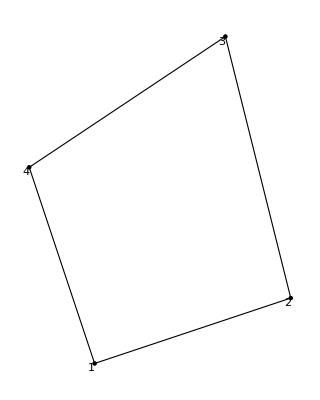

(0.407005 | 0.104972 | -0.300742 | -0.139621 | -0.0902343 | -0.115496 | -0.0160288 | 0.150145
0.104972 | 0.545515 | -0.0729543 | -0.0286192 | -0.115496 | -0.277013 | 0.0834783 | -0.239883
-0.300742 | -0.0729543 | 0.702964 | -0.142679 | 0.0518507 | 0.0812231 | -0.454073 | 0.13441
-0.139621 | -0.0286192 | -0.142679 | 0.393915 | 0.14789 | -0.182347 | 0.13441 | -0.182949
-0.0902343 | -0.115496 | 0.0518507 | 0.14789 | 0.316499 | 0.107979 | -0.278116 | -0.140373
-0.115496 | -0.277013 | 0.0812231 | -0.182347 | 0.107979 | 0.4688 | -0.073706 | -0.00944048
-0.0160288 | 0.0834783 | -0.454073 | 0.13441 | -0.278116 | -0.073706 | 0.748217 | -0.144182
0.150145 | -0.239883 | 0.13441 | -0.182949 | -0.140373 | -0.00944048 | -0.144182 | 0.432273)

```mathematica
order=1;
young=1;
nu=0.25;
eltype=1;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
allcoords={{{2,1},{5,2},{4,6},{1,4}}}
topol={{1,2,3,4}}
eltype=1;
forcing=0.;
nnodes={{2,1},{5,2},{4,6},{1,4}};
meshVis1=Graphics[{FaceForm[],EdgeForm[Black],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];
nodeVis=Graphics[{Black,PointSize[Medium],Point[nnodes]}];
nodeVis2=Graphics[{MapIndexed[Text[#2[[1]],#1,{2,2}]&,nnodes],{Black,Point[nnodes]}}];
Show[meshVis1,nodeVis,nodeVis2]
{kE,fE}=Assemble[allcoords,nnodes,topol,order,eltype];
MatrixForm[kE]
```

```mathematica
order=2;
young=1;
eltype=1;
nu=0.25;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
allcoords={{{0,0},{1,0},{1,1},{0,1},{0.5,0.1},{1.1,0.5},{0.5,1.1},{0.1,0.5},{0.6,0.6}}};
nnodes=Flatten[allcoords,1];
topol={{1,2,3,4,5,6,7,8,9}};
forcing=0.;
{KE,FE}=Assemble[allcoords,nnodes,topol,order,eltype];
MatrixForm[KE]
```

(0.300523 | 0.0641471 | -0.00406102 | 0.00580932 | -0.0182484 | -0.0186238 | -0.0705443 | -0.0164129 | -0.297688 | -0.0188103 | 0.0479151 | 0.0673114 | 0.0616122 | 0.0673114 | 0.0146412 | 0.0700785 | -0.0341501 | -0.220811
0.0641471 | 0.300523 | -0.0164129 | -0.0705443 | -0.0186238 | -0.0182484 | 0.00580932 | -0.00406102 | 0.0700785 | 0.0146412 | 0.0673114 | 0.0616122 | 0.0673114 | 0.0479151 | -0.0188103 | -0.297688 | -0.220811 | -0.0341501
-0.00406102 | -0.0164129 | 0.380042 | -0.140819 | -0.0570223 | 0.0216762 | -0.0182484 | 0.0191023 | -0.278482 | 0.147235 | -0.022493 | -0.155006 | 0.0603432 | -0.0682683 | 0.0929883 | -0.0826742 | -0.153066 | 0.275166
0.00580932 | -0.0705443 | -0.140819 | 0.558468 | -0.000545998 | 0.0256815 | 0.0191023 | -0.0182484 | 0.0583465 | -0.00179537 | -0.0661171 | -0.324008 | -0.0682683 | 0.0473381 | -0.0826742 | 0.160754 | 0.275166 | -0.377645
-0.0182484 | -0.0186238 | -0.0570223 | -0.000545998 | 0.776433 | 0.333284 | 0.0256815 | 0.0216762 | 0.159485 | 0.0817172 | -0.018749 | 0.00552764 | -0.371132 | -0.0833613 | 0.0924113 | 0.0817172 | -0.588859 | -0.421391
-0.0186238 | -0.0182484 | 0.0216762 | 0.0256815 | 0.333284 | 0.776433 | -0.000545998 | -0.0570223 | 0.0817172 | 0.0924113 | -0.0833613 | -0.371132 | 0.00552764 | -0.018749 | 0.0817172 | 0.159485 | -0.421391 | -0.588859
-0.0705443 | 0.00580932 | -0.0182484 | 0.0191023 | 0.0256815 | -0.000545998 | 0.558468 | -0.140819 | 0.160754 | -0.0826742 | 0.0473381 | -0.0682683 | -0.324008 | -0.0661171 | -0.00179537 | 0.0583465 | -0.377645 | 0.275166
-0.0164129 | -0.00406102 | 0.0191023 | -0.0182484 | 0.0216762 | -0.0570223 | -0.140819 | 0.380042 | -0.0826742 | 0.0929883 | -0.0682683 | 0.0603432 | -0.155006 | -0.022493 | 0.147235 | -0.278482 | 0.275166 | -0.153066
-0.297688 | 0.0700785 | -0.278482 | 0.0583465 | 0.159485 | 0.0817172 | 0.160754 | -0.0826742 | 1.55088 | -0.188714 | -0.376261 | -0.274477 | -0.123815 | -0.00382787 | -0.592551 | 0.42453 | -0.202317 | -0.0849787
-0.0188103 | 0.0146412 | 0.147235 | -0.00179537 | 0.0817172 | 0.0924113 | -0.0826742 | 0.0929883 | -0.188714 | 1.80586 | -0.274477 | -0.15445 | -0.00382787 | 0.101332 | 0.42453 | -0.592551 | -0.0849787 | -1.35844
0.0479151 | 0.0673114 | -0.022493 | -0.0661171 | -0.018749 | -0.0833613 | 0.0473381 | -0.0682683 | -0.376261 | -0.274477 | 1.58951 | 0.104501 | -0.0304582 | 0.22395 | 0.101332 | -0.00382787 | -1.33813 | 0.10029
0.0673114 | 0.0616122 | -0.155006 | -0.324008 | 0.00552764 | -0.371132 | -0.0682683 | 0.0603432 | -0.274477 | -0.15445 | 0.104501 | 1.075 | 0.22395 | -0.0304582 | -0.00382787 | -0.123815 | 0.10029 | -0.193086
0.0616122 | 0.0673114 | 0.0603432 | -0.0682683 | -0.371132 | 0.00552764 | -0.324008 | -0.155006 | -0.123815 | -0.00382787 | -0.0304582 | 0.22395 | 1.075 | 0.104501 | -0.15445 | -0.274477 | -0.193086 | 0.10029
0.0673114 | 0.0479151 | -0.0682683 | 0.0473381 | -0.0833613 | -0.018749 | -0.0661171 | -0.022493 | -0.00382787 | 0.101332 | 0.22395 | -0.0304582 | 0.104501 | 1.58951 | -0.274477 | -0.376261 | 0.10029 | -1.33813
0.0146412 | -0.0188103 | 0.0929883 | -0.0826742 | 0.0924113 | 0.0817172 | -0.00179537 | 0.147235 | -0.592551 | 0.42453 | 0.101332 | -0.00382787 | -0.15445 | -0.274477 | 1.80586 | -0.188714 | -1.35844 | -0.0849787
0.0700785 | -0.297688 | -0.0826742 | 0.160754 | 0.0817172 | 0.159485 | 0.0583465 | -0.278482 | 0.42453 | -0.592551 | -0.00382787 | -0.123815 | -0.274477 | -0.376261 | -0.188714 | 1.55088 | -0.0849787 | -0.202317
-0.0341501 | -0.220811 | -0.153066 | 0.275166 | -0.588859 | -0.421391 | -0.377645 | 0.275166 | -0.202317 | -0.0849787 | -1.33813 | 0.10029 | -0.193086 | 0.10029 | -1.35844 | -0.0849787 | 4.24569 | 0.0612459
-0.220811 | -0.0341501 | 0.275166 | -0.377645 | -0.421391 | -0.588859 | 0.275166 | -0.153066 | -0.0849787 | -1.35844 | 0.10029 | -0.193086 | 0.10029 | -1.33813 | -0.0849787 | -0.202317 | 0.0612459 | 4.24569)

{{{0,0},{120,0},{120,160}},{{0,0},{120,160},{0,160}}}

{{1,2,3},{1,3,4}}

{{0,0},{120,0},{120,160},{0,160}}

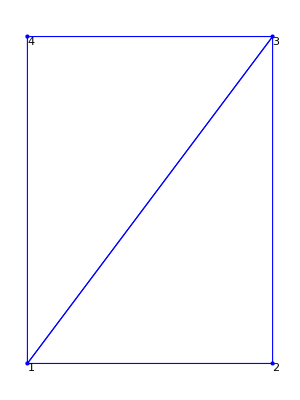

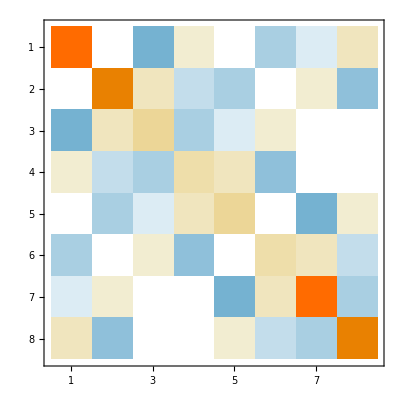

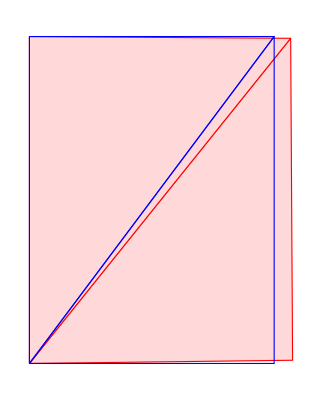

{0,0,11.2911,1.96367,10.1129,-1.08002,0,0}

```mathematica
order=1;
h=0.036;(*inch*)young=30 10^6 h;
nu=0.25;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
allcoords={{{0,0},{120,0},{120,160}},{{0,0},{120,160},{0,160}}}(*inch*)
topol={{1,2,3},{1,3,4}}
eltype=2;
forcing=0.;
nnodes={{0,0},{120,0},{120,160},{0,160}}
meshVis1=Graphics[{FaceForm[],EdgeForm[Blue],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3}]]]]}];
nodeVis=Graphics[{MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Blue,Point[nnodes]}}];
mesh1=Show[meshVis1,nodeVis]
{KE,FE}=Assemble[allcoords,nnodes,topol,order,eltype];
BIG=10^12;
KE=ApplyNodeBCDisplacement[KE,{1,4},{{{BIG,1},{1,BIG}},{{BIG,1},{1,BIG}}}];
FE=ApplyNodeBCForce[FE,{2,3},{{800,0},{800,0}}];
MatrixPlot[KE]
sol=LinearSolve[KE,FE,Method->"Cholesky"];
scale=8000;
deformed=(Flatten[nnodes]+scale sol);
tabdeformed=Table[{deformed[[i]],deformed[[i+1]]},{i,1,Length[deformed],2}];
meshVisDef=Graphics[{FaceForm[{LightRed,Opacity[3]}],EdgeForm[Red],GraphicsComplex[tabdeformed,Polygon[topol[[All,{1,2,3}]]]]}];
Show[meshVisDef,meshVis1]
10^4 sol//Chop
```

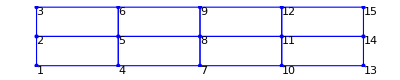

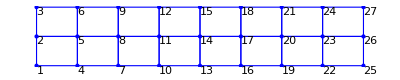

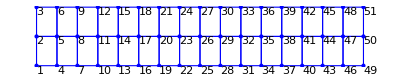

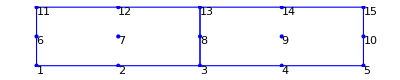

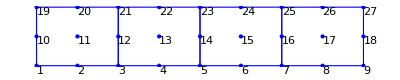

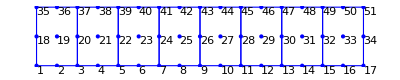

| Linear | Reference | Quadratic | Reference
15 nodes | 0.3104 | 0.3134 | 0.4973 | 0.5031
27 nodes | 0.435 | 0.4388 | 0.5086 | 0.5129
51 nodes | 0.484 | 0.4878 | 0.5104 | 0.5137

```mathematica
eltype=1;
order=1;h=1;a=10;b=2;young=30 10^6;(*Young modulus-psi*)nu=0.25;mu=young/(2(1+nu));lambda=young nu/((1+nu)(1-2nu));(*Lamé Constants-psi*)(*Mesh Generation and visualization*)order1=1;
{allcoords1,meshnodes1,meshtopology1}=GenerateGridMesh[a,b,5,3,order1];
{allcoords2,meshnodes2,meshtopology2}=GenerateGridMesh[a,b,9,3,order1];
{allcoords3,meshnodes3,meshtopology3}=GenerateGridMesh[a,b,17,3,order1];
{meshvis1,nodevis1}=GenerateGraphics[meshnodes1,meshtopology1,order1];
{meshvis2,nodevis2}=GenerateGraphics[meshnodes2,meshtopology2,order1];
{meshvis3,nodevis3}=GenerateGraphics[meshnodes3,meshtopology3,order1];
Show[meshvis1,nodevis1]
Show[meshvis2,nodevis2]
Show[meshvis3,nodevis3]
order2=2;
{allcoords4,meshnodes4,meshtopology4}=GenerateGridMesh[a,b,3,2,order2];
{allcoords5,meshnodes5,meshtopology5}=GenerateGridMesh[a,b,5,2,order2];
{allcoords6,meshnodes6,meshtopology6}=GenerateGridMesh[a,b,9,2,order2];
{meshvis4,nodevis4}=GenerateGraphics[meshnodes4,meshtopology4,order2];
{meshvis5,nodevis5}=GenerateGraphics[meshnodes5,meshtopology5,order2];
{meshvis6,nodevis6}=GenerateGraphics[meshnodes6,meshtopology6,order2];
Show[meshvis4,nodevis4]
Show[meshvis5,nodevis5]
Show[meshvis6,nodevis6]
(*Stiffness Matrix and Load Vector Assembling*)
{K1,F1}=Assemble[allcoords1,meshnodes1,meshtopology1,order1,eltype];
{K2,F2}=Assemble[allcoords2,meshnodes2,meshtopology2,order1,eltype];
{K3,F3}=Assemble[allcoords3,meshnodes3,meshtopology3,order1,eltype];
{K4,F4}=Assemble[allcoords4,meshnodes4,meshtopology4,order2,eltype];
{K5,F5}=Assemble[allcoords5,meshnodes5,meshtopology5,order2,eltype];
{K6,F6}=Assemble[allcoords6,meshnodes6,meshtopology6,order2,eltype];
(*Imposing Boundary Conditions*)
(*Force Vector*)
F1=ApplyNodeBCForce[F1,{1,2,3},{{0,-75},{0,-150},{0,-75}}];
F2=ApplyNodeBCForce[F2,{1,2,3},{{0,-75},{0,-150},{0,-75}}];
F3=ApplyNodeBCForce[F3,{1,2,3},{{0,-75},{0,-150},{0,-75}}];
F4=ApplyNodeBCForce[F4,{1,6,11},{{0,-50},{0,-200},{0,-50}}];
F5=ApplyNodeBCForce[F5,{1,10,19},{{0,-50},{0,-200},{0,-50}}];
F6=ApplyNodeBCForce[F6,{1,18,35},{{0,-50},{0,-200},{0,-50}}];
(*Null Displacement*)
BIG=10^12;
K1=ApplyNodeBCDisplacement[K1,{13,14,15},{{{BIG,1},{1,BIG}},{{BIG,1},{1,BIG}},{{BIG,1},{1,BIG}}}];
K2=ApplyNodeBCDisplacement[K2,{25,26,27},{{{BIG,1},{1,BIG}},{{BIG,1},{1,BIG}},{{BIG,1},{1,BIG}}}];
K3=ApplyNodeBCDisplacement[K3,{49,50,51},{{{BIG,1},{1,BIG}},{{BIG,1},{1,BIG}},{{BIG,1},{1,BIG}}}];
K4=ApplyNodeBCDisplacement[K4,{5,10,15},{{{BIG,1},{1,BIG}},{{BIG,1},{1,BIG}},{{BIG,1},{1,BIG}}}];
K5=ApplyNodeBCDisplacement[K5,{9,18,27},{{{BIG,1},{1,BIG}},{{BIG,1},{1,BIG}},{{BIG,1},{1,BIG}}}];
K6=ApplyNodeBCDisplacement[K6,{17,34,51},{{{BIG,1},{1,BIG}},{{BIG,1},{1,BIG}},{{BIG,1},{1,BIG}}}];
(*Solving Linear System*)
sol1=LinearSolve[K1,F1,Method->"Cholesky"];sol2=LinearSolve[K2,F2,Method->"Cholesky"];sol3=LinearSolve[K3,F3,Method->"Cholesky"];
sol4=LinearSolve[K4,F4,Method->"Cholesky"];sol5=LinearSolve[K5,F5,Method->"Cholesky"];sol6=LinearSolve[K6,F6,Method->"Cholesky"];
TableForm[{{"","Linear","Reference","Quadratic","Reference"},{"15 nodes",SetPrecision[-sol1[[2 2]]100,4],0.3134,SetPrecision[-sol4[[6 2]]100,4],0.5031},{"27 nodes",SetPrecision[-sol2[[2 2]]100,4],0.4388,SetPrecision[-sol5[[10 2]]100,4],0.5129},{"51 nodes",SetPrecision[-sol3[[2 2]]100,4],0.4878,SetPrecision[-sol6[[18 2]]100,4],0.5137}}]
```

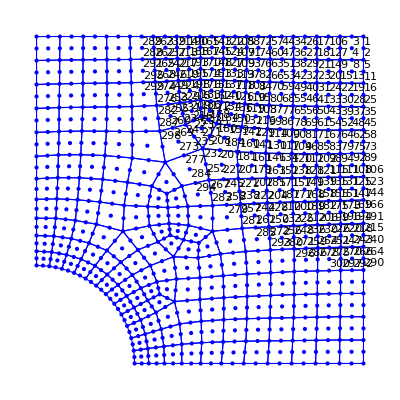

-Graphics-

```mathematica
pack=Developer`ToPackedArray;
topol=pack@Transpose@Drop[Transpose@Import["C:\\Paper-Diogo-Thiago\\elschapacomfuroleft.txt","Table"],1];
nnodesAll=Import["C:\\Paper-Diogo-Thiago\\noschapacomfuroleft.txt","Table"];
nnodes=pack@N[nnodesAll[[All,{2,3}]]];
allcoords=ParallelTable[nnodes[[topol[[i]][[j]]]],{i,1,Length[topol]},{j,1,9}];
(*edges are straight*)
meshVis1=Graphics[{FaceForm[],EdgeForm[Blue],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];
nodeVis=Graphics[{MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Blue,Point[nnodes]}}];
mesh=Show[meshVis1,nodeVis]
h=1;
order=2;
eltype=1;
forcing=0.;
young=205000;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
eltype=1;
(*AbsoluteTiming[Assemble[allcoords,topol,order,forcing,eltype];]*)
{KE,FE}=Assemble[allcoords,nnodes,topol,order,eltype];
matrix=MatrixPlot[KE]
```

```mathematica
FindIds[nodes_,coords_]:=Block[{nodestofind=Nearest[nodes,coords][[All,1]]},Flatten[Position[nodes,Alternatives@@nodestofind]]]
```

```mathematica
nodetofind={{300,0},{0,300}};
{hole1,hole2}=FindIds[nnodes,nodetofind]
nodetofind={{300,0},{1000,0}};
{inferiorline1,inferiorline2}=FindIds[nnodes,nodetofind]
nodetofind={{0,300},{0,1000}};
{leftline1,leftline2}=FindIds[nnodes,nodetofind]
```

{870,871}

{644,870}

{645,871}

```mathematica
FindLineElemens[id1_,id2_,nnodes_,order_]:=Block[{h1,h2,allids,Flag,A,B,tol,i,ids,nodesvec,linenodes,temp1,temp2,elsvec,idsvec,nodes,newout,norm},
A=nnodes[[id1]];
B=nnodes[[id2]];
tol=10^-3;
linenodes={};
ids={};
nodesvec={};
elsvec={};
Flag=True;
h1=Sqrt[A[[1]]A[[1]]+A[[2]]A[[2]]];
h2=Sqrt[B[[1]]B[[1]]+B[[2]]B[[2]]];
For[i=1,i≤Length[nnodes],i++,
(*Vertical Line*)
If[Abs[A[[1]]-B[[1]]]<tol && Abs[nnodes[[i]][[1]]-A[[1]]]<tol,
If[Between[nnodes[[i]][[2]],{{A[[2]],B[[2]]},{B[[2]],A[[2]]}}],
AppendTo[linenodes,{nnodes[[i]],i}];
];
Flag=False;
,
(*Horizontal Line*)
If[Abs[A[[2]]-B[[2]]]<tol&& Abs[nnodes[[i]][[2]]-A[[2]]]<tol,
If[Between[nnodes[[i]][[1]],{{A[[1]],B[[1]]},{B[[1]],A[[1]]}}],
AppendTo[linenodes,{nnodes[[i]],i}];

];
Flag=False;
,
norm=Norm[nnodes[[i]]];
If[(Abs[norm-h1])<tol&&Abs[norm-h2]<tol  &&Flag≠False,
AppendTo[linenodes,{nnodes[[i]],i}];
 ];
];
];
];
newout=Transpose[SortBy[linenodes,Smaller]];
allids=newout[[2]];
nodes={};
ids={};
idsvec={};
nodesvec={};
Table[
AppendTo[nodes,newout[[1,i]]];
AppendTo[ids,newout[[2,i]]];
If[Length[ids]==order+1,
AppendTo[nodesvec,nodes];
AppendTo[idsvec,ids];
temp1=ids[[order+1]];
temp2=nodes[[order+1]];
nodes={};
ids={};
AppendTo[ids,temp1];
AppendTo[nodes,temp2];
];
,{i,1,Length[linenodes]}];
{nodesvec,idsvec,allids}
];
```

```mathematica
ContributeLineDirichlet[EK_,EF_,nodes_,id1_,id2_,ek_,ef_,order_]:=Block[{nodevec,idsvec,x1,x2,y1,y2,Ef=EF,Ek=EK,els,ids,el,i,shapes,xx,J,xi,xix,w,integralxi1,vecPtosPesos,co,newco,j,k},
{nodevec,idsvec,ids}=FindLineElemens[id1,id2,nodes,order];
idsd2=ids;
el=Length[ids];
For[i=1,i≤el,i++,
For[j=1,j≤2,j++,
For[k=1,k≤2,k++,
Ek[[2ids[[i]] +j-2,2ids[[i]]+k-2 ]]*=ek[[j,k]];
];
Ef[[2ids[[i]] +j-2]]=ef[[j]];
];
];
{Ek,Ef}
];
```

```mathematica
ComputeShape[order_,var_]:=Block[{npoints},
npoints=order+1;
tab3[i_,n_]:=Table[If[j==i,1,0],{j,1,n}];
poli3[j_,n_]:=Table[{-1+2 (i-1)/(n-1),tab3[j,n][[i]]},{i,1,n}];
ListPoli[n_]:=Table[InterpolatingPolynomial[poli3[i,n],var],{i,1,n}];
ListPoli[npoints]
]
```

```mathematica
ComputeNormals[pt_]:=Block[{lines,x,delta,intdata,R=300,normal,v},
Clear[r];
rr[x_]=-x/(√(R^2-0.999999999999999 x^2));

pervec[v_]:={-v[[2]]/Norm[v],v[[1]]/Norm[v]};
lines=rr[pt[[1]]](x-pt[[1]])+ pt[[2]];
delta=10^-8;
normal=({pt[[1]]+delta,lines/.x->pt[[1]]+delta}-{pt[[1]],lines/.x->pt[[1]]})/Norm[({pt[[1]]+delta,lines/.x->pt[[1]]+delta}-{pt[[1]],lines/.x->pt[[1]]})];
pervec[normal]
]
```

```mathematica
ContributeLineNewmanPressure[EF_,fx_,nodes_,order_,id1_,id2_]:=Block[{vecnodes,idsvec,ids,normal,coordinates,temp=0,co,el,i,shapes,xi,x0,y0,xf,yf,h,cos,sin,vertOrHor,x,J,vecPtosPesos,xix,w,integral,Ef=EF},
sumx=0.;
sumy=0.;
{vecnodes,idsvec,ids}=FindLineElemens[id1,id2,nodes,order];
vecdata=vecnodes;
(*Print["id1 = ",id1];
Print["id2 = ",id2];
Print["vecnodes = ",vecnodes];*)
el=Length[vecnodes];
shapes=ComputeShape[order,xi];
For[i=1,i≤el,i++,
coordinates=Table[0,{order+1}];
co=vecnodes[[i]];
x0=co[[1,1]];
xf=co[[Length[co],1]];
y0=co[[1,2]];
yf=co[[Length[co],2]];
h=Sqrt[(xf-x0)^2 +(yf-y0)^2];
cos=(xf-x0)/h;
sin=(yf-y0)/h;
temp=0;
Table[
coordinates[[k]]=temp;
temp+=h/order;
,{k,1,order+1}
];
(*teste=ComputeNormals[co];*)
x=Sum[shapes[[i]] coordinates[[i]],{i,1,order+1}];
J=D[x,xi];
vecPtosPesos=GaussianQuadratureWeights[order+1,-1,1];
{xix,w}=Transpose[vecPtosPesos];
integral=Table[Sum[((fx[co[[j]]]shapes[[j]]J)/.xi->xix[[i]]) w[[i]],{i,1,Length[xix]}],{j,1,Length[shapes]}];
Table[
normal=ComputeNormals[vecnodes[[i]][[j]]];
Ef[[ idsvec[[i,j]] 2-1]]+=integral[[j]]normal[[1]];
Ef[[ idsvec[[i,j]] 2]]+=integral[[j]]normal[[2]];
,{j,1,order+1}];
];
Ef
];
```

-5995.72

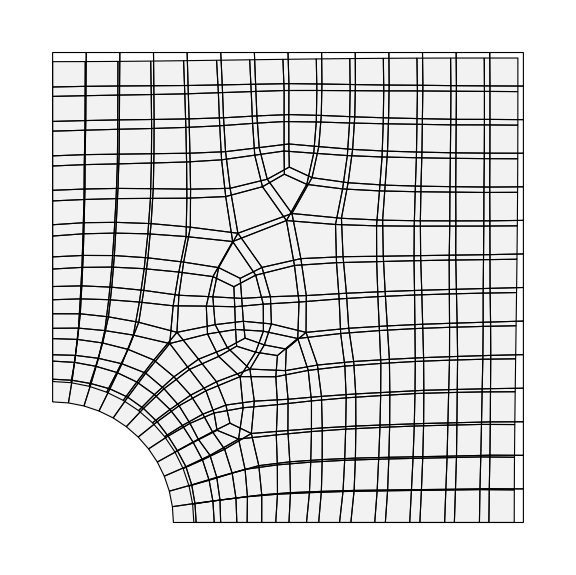

```mathematica
FE=Table[0,{Length[KE]}];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,inferiorline1,inferiorline2,{{1,1},{1,10^12}},{0,0},order];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,leftline1,leftline2,{{10^12,1},{1,1}},{0,0},order];
f[pt_]:=-10;
(*FE=ContributeLineNewman[FE,f,nnodes,order,hole1,hole2];*)
FE=ContributeLineNewmanPressure[FE,f,nnodes,order,hole2,hole1];
Sum[FE[[i]],{i,1,Length[FE]}]
sol=LinearSolve[KE,FE,Method->"Banded"];
scale=2000;
deformed=(Flatten[nnodes]+scale sol);
tabdeformed=ParallelTable[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];
meshVis1=Graphics[{FaceForm[],EdgeForm[{Dashed}],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];
meshVisDef=Graphics[{FaceForm[{Gray,Opacity[0.1]}],EdgeForm[Black],GraphicsComplex[tabdeformed,Polygon[topol[[All,{1,2,3,4}]]]]}];
defplussundef=Show[meshVisDef,meshVis1,ImageSize->Large]
```

```mathematica
ComputeSol[topol_,coords_,order_,coefs_,eltype_]:=Block[{X,InvJ,GradPhi,GradPsi,nels,dsol,xa,xb,k=0,i,phi,sol,phisz,j,xx,J,co,h,x=0,psis,id,y=0,xi,eta,Jac,DetJac,kk},
{psis,GradPsi}=Compute2DShape[order,eltype];
nels=Length[topol];
sol=Table[0,{nels},{2}];
X=Table[0,{nels},{2}];
dsol=Table[0,{nels},{4}];
Table[
x=0.;
y=0.;
kk=Length[psis];
Table[
id=topol[[i,j]];
x+=coords[[id,1]] psis[[j]];
y+=coords[[id,2]] psis[[j]];
,{j,1,kk}];
Jac={{D[x,xi],D[y,xi]},{D[x,eta],D[y,eta]}};
DetJac=Det[Jac];
InvJ=Inverse[Jac];
GradPhi=InvJ.GradPsi;
Table[
id=topol[[i,j]];
sol[[i,1]]+=(psis[[j]] coefs[[2 id-1]] );
sol[[i,2]]+=(psis[[j]] coefs[[2id]] );
(*duxdx*)
dsol[[i,1]]+=(GradPhi[[1,j]]coefs[[2 id-1]] );
(*duxdy*)
dsol[[i,2]]+=(GradPhi[[2,j]] coefs[[2id-1]] );
(*duydx*)
dsol[[i,3]]+=(GradPhi[[1,j]]coefs[[2id]] );
(*duydy*)
dsol[[i,4]]+=(GradPhi[[2,j]] coefs[[2id]] );
,{j,1,kk}];
X[[i,1]]=x;
X[[i,2]]=y;
,{i,1,nels}];
{sol,dsol,X}
]
```

```mathematica
ComputeStress[dsol_,young_,nu_]:=Block[{strain,gradu,lambda=young nu/((1+nu)(1-2 nu)),mu=young/(2(1+nu)),dudx,dudy,dvdx,dvdy,i,eps,stress,ex,ey,exy,C},

strain=Table[0,{Length[dsol]}];
stress=Table[0,{Length[dsol]}];
For[i=1,i≤Length[dsol],i++,
{dudx,dudy,dvdx,dvdy}=dsol[[i]];
ex=dudx;
ey=dvdy;
exy=(dudy+dvdx);
strain={ex,ey,exy};
C=Table[0,{3},{3}];
C[[1,1]]=young/(1-nu^2);
C[[1,2]]=nu young/(1-nu^2);
C[[2,1]]=C[[1,2]];
C[[2,2]]=C[[1,1]];
C[[3,3]]=young/(2 (1+nu));
stress[[i]]=C.strain;
];
{stress,strain}
];
```

```mathematica
computesollist[X_,sols_,sx_]:=Block[{refine,sollists,v,x,y,s,sollist},
sollists={};
refine=1/3.;
v=Table[{xi,eta},{xi,0,1,refine},{eta,1-xi,0,refine}];

refine=1/2.;
v=Table[{xi,eta},{xi,-1,1,refine},{eta,-1,1,refine}];
sollists=Table[0,{Length[X]}];
Table[
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Sol[xii_,etaa_]:=sols[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Sol[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
sollist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
sollists[[i]]=sollist;
,{i,1,Length[X]}];
sollists
]
```

```mathematica
{sols,dsols,X}=ComputeSol[topol,nnodes,order,sol,eltype]//Simplify//Chop;
stress=ComputeStress[dsols,young,nu][[1]];
```

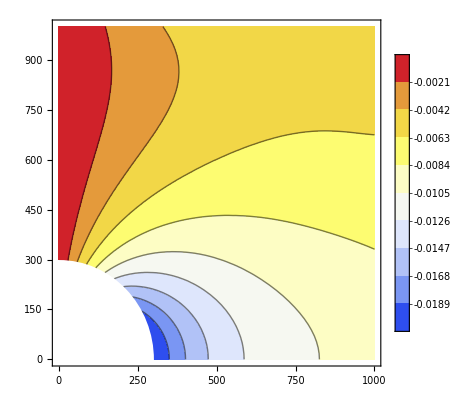

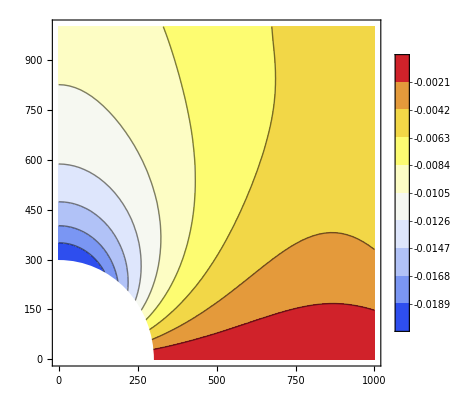

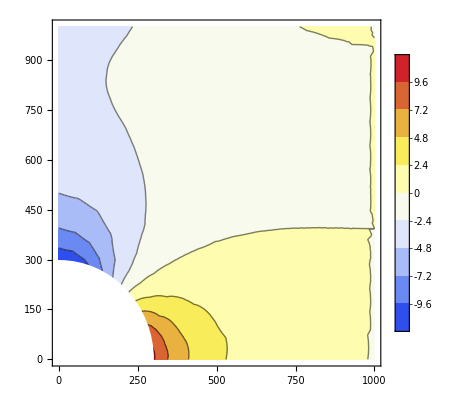

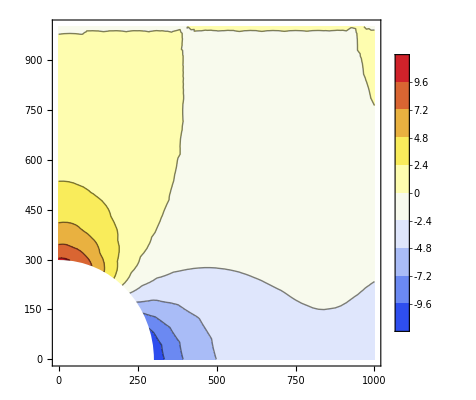

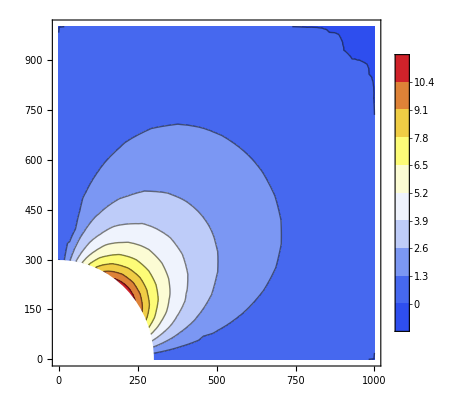

```mathematica
lpd=Show[Graphics[{GrayLevel[1],Disk[{0,0},300]},AspectRatio->Automatic]];
tabux=computesollist[X,sols,1];
tabuy=computesollist[X,sols,2];
tabsx=computesollist[X,stress,1];
tabsy=computesollist[X,stress,2];
tabsxy=computesollist[X,stress,3];
lpux=ListContourPlot[Flatten[tabux,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->9];
lpuy=ListContourPlot[Flatten[tabuy,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->9];
lpsx=ListContourPlot[Flatten[tabsx,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->9,PlotRange->{-12,12}];
lpsy=ListContourPlot[Flatten[tabsy,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->9,PlotRange->{-12,12}];
lpsxy=ListContourPlot[Flatten[tabsxy,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->9,PlotRange->{-1,12}];
lpux=Show[lpux,lpd]
lpuy=Show[lpuy,lpd]
lpsx=Show[lpsx,lpd]
lpsy=Show[lpsy,lpd]
lpsxy=Show[lpsxy,lpd]
```